```mathematica
PS[n_] := PS[n]= FullSimplify[MangoldtLambda[ n]/Log[n]]
```

```mathematica
DD[n_, k_, a_] :=  DD[n,k,a] = Sum[ PS[j](a^k/k! + DD[n/j, k+1,a]), {j,2,n}]
```

```mathematica
Dd[ n_, a_ ]:= Dd[n,a] = DD[n,1,a]-DD[n-1,1,a]
Dd[ 1, a_ ]:= 1
```

```mathematica
D2[n_,k_] := Sum[ D2[n/j, k-1], {j,2,n}]
```

```mathematica
D2[n_,0] := 1
```

```mathematica
Dd2[ n_, k_] := D2[n,k] - D2[n-1,k]
```

```mathematica
Ds[ n_, k_ ] := Sum[ (-1)^j Binomial[k, k-j] Dd[ n, k-j], {j, 0, 50000 }]
```

```mathematica
Ds[ 8, 2]
```

2

```mathematica
DA[ n_, k_, j_] :=(-1)^j Binomial[k, k-j] Dd[ n, k-j]
DB[ n_, k_, j_] :=  Binomial[k, k-j] Dd[ n, k-j]
DR[ n_, k_ ] := Sum[  Binomial[k, k-j] Dd[ n, k-j], {j, 0, 3000 }]
```

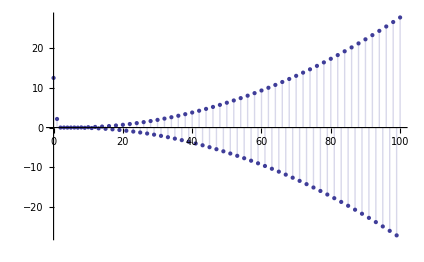

```mathematica
DiscretePlot[DB[72,2.02, j],{j,0, 100,1}]
```

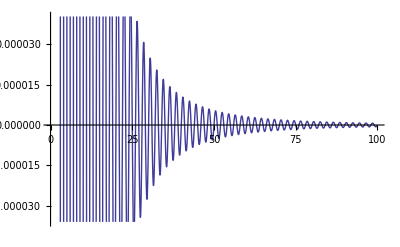

```mathematica
Plot[ Binomial[ 2, 2-x], {x,0,100}]
```

```mathematica
Binomial[4,4-100.1]
```

2.59971×10^-10

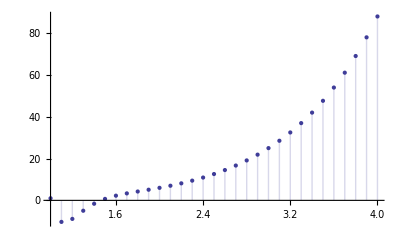

```mathematica
DiscretePlot[DR[8,j],{j,1, 4,.1}]
```

```mathematica
Dd[2,.000000001]/.000000001
```

```mathematica
0.9999999999999999
```

```mathematica
Sum[ Dd[j,0], {j,Divisors[24]}]
```

1

```mathematica
Dd[24,1]
```

1

```mathematica
Dd[4,0]
```

```mathematica
Sum[ MoebiusMu[ 7/j]Dd[j,1.000000001], {j,Divisors[7]}]/.000000001
```

1.

```mathematica
Dd[7,.000000001]/.000000001
```

```mathematica
0.9999999999999998
FF[n_] := Sum[ MoebiusMu[ n/j]Dd[j,1.000000001], {j,Divisors[n]}]/.000000001
```

1.

```mathematica
FF[10]
```

```mathematica
FE[n_] := N[Sum[ MoebiusMu[j]Dd[n/j,1 + 10^-240], {j,Divisors[n]}]/10^-240]
```

```mathematica
FE[101]
```

1.

```mathematica
FD[n_] := N[Sum[ MoebiusMu[j], {j,Divisors[n]}]/10^-240]
```

```mathematica
FD[8]
```

0.

```mathematica
Dd[12,1 + 10^-400]
```

2000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000500000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000040000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001/2000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
FG[n_] := N[Sum[ MoebiusMu[j]Dd[n/j,1 + 10^-400000], {j,Divisors[n]}]/10^-400000]
```

```mathematica
Table[ FG[i], {i,2,10}]
```

{1.,1.,0.5,1.,1.×10^-400000,1.,0.333333,0.5,1.×10^-400000}

```mathematica
FH[n_] := Sum[ MoebiusMu[j]Dd[n/j,1], {j,Divisors[n]}]
```

```mathematica
Table[ FH[i], {i,1,10}]
```

{1,0,0,0,0,0,0,0,0,0}

```mathematica
FI[n_] := Sum[ MoebiusMu[j](DD[n/j,1,1.001]), {j,1,n}]/.001
```

```mathematica
N[FI[96]]
```

-972.423

```mathematica
MoebiusMu[1]
```

1

```mathematica
ClearSystemCache
```

```mathematica
ClearSystemCache[]
```

```mathematica
Table[ FullSimplify[MoebiusMu[j](DD[100/j,1,1 + 10^-7])/10^-7], {j,1,100}]
```

{7920001596133441897781029444490722222492222223/8000000000000000000000000000000000000,-98000018056667722500025333333575000001/200000000000000000000000000000,-128000022146667813333355833333466666667/400000000000000000000000000000,0,-1520000243333344100000166666667/8000000000000000000000,1200000187333340900000086666667/8000000000000000000000,-6500000966666701666667/50000000000000,0,0,18000002566666746666667/200000000000000,-16000002166666726666667/200000000000000,0,-1200000150000003/20000000,1200000150000003/20000000,1000000130000003/20000000,0,-800000090000001/20000000,0,-800000090000001/20000000,0,600000070000001/20000000,600000070000001/20000000,-600000070000001/20000000,0,0,20000002,0,0,-20000002,-20000002,-20000002,0,20000002,10000001,10000001,0,-10000001,10000001,10000001,0,-10000001,-10000001,-10000001,0,0,10000001,-10000001,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
DMM[n_, k_, a_] :=  DMM[n,k,a] = Sum[ PS[j](a^k/k! - DMM[n/j, k+1,a]), {j,2,n}]
DM[ n_, a_ ]:= DMM[n,1,a]
```

```mathematica
Dm[ n_, a_ ]:= Dm[n,a] = -DM[n,a]+DM[n-1,a]
Dm[ 1, a_ ]:= 1
```

```mathematica
Table[Dm[n,1], {n,1,100}]
```

{1,-1,-1,0,-1,1,-1,0,0,1,-1,0,-1,1,1,0,-1,0,-1,0,1,1,-1,0,0,1,0,0,-1,-1,-1,0,1,1,1,0,-1,1,1,0,-1,-1,-1,0,0,1,-1,0,0,0,1,0,-1,0,1,0,1,1,-1,0,-1,1,0,0,1,-1,-1,0,1,-1,-1,0,-1,1,0,0,1,-1,-1,0,0,1,-1,0,1,1,1,0,-1,0,1,0,1,1,1,0,-1,0,0,0}

```mathematica
Table[ MoebiusMu[n]-Dm[n,1], {n,1,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
FL[n_] := N[-Sum[Dm[j,1 + 10^-400]/10^-400, {j,Divisors[n]}]]
```

```mathematica
Table[ FL[i], {i,2,10}]
```

{1.,1.,0.5,1.,-1.×10^-400,1.,0.333333,0.5,-1.×10^-400}

```mathematica
FL[3]
```

```mathematica
Dm[3,1+10^-400000]
```

```mathematica
DD[200,1,-1]
```

-9

```mathematica
DM[200,1]
```

9

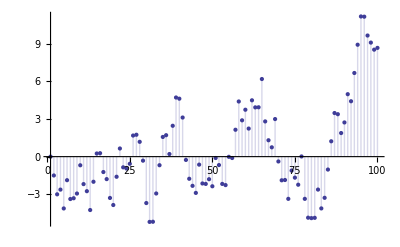

```mathematica
DiscretePlot[ DD[n,1,-1.5], {n,1,100}]
```

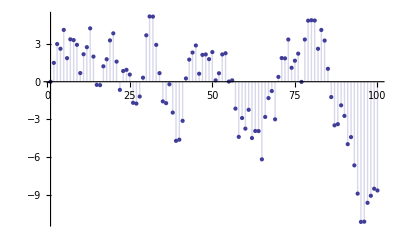

```mathematica
DiscretePlot[ DM[n,1.5], {n,1,100}]
```

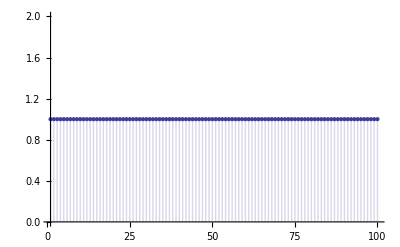

```mathematica
DiscretePlot[ 1+DD[n,1,1.5]+DM[n,-1.5], {n,1,100}]
```

```mathematica
FR[n_] := Sum[ (DM[n/j,1.000001]), {j,1,n}]/.000001
```

```mathematica
N[FR[100]]
```

9.9×10^7